# H_2 dynamics: recompilation vs Trotter

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

## modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->{a Subscript[Id, 0]}};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->2000,Method->"RandomSearch"];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]


distMatrices::usage="distMatrices[M1,M2,subspace], return <|fullopt->dfullopt,subopt->dsubopt,fullsubopt->dfullsubopt|> "
distMatrices[M1_,M2_,subspace_]:=Module[{globalphase,mindist,fullopt,subopt,fullsubopt,dsubopt,dfullopt,dfullsubopt,ϕ,dynmat},
subopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
fullopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
fullsubopt[ϕ_?NumericQ]:=Max[Re[Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]][[1+subspace]]];

{dfullopt,globalphase}=NMinimize[{fullopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->2000,Method->"RandomSearch"];
If[Length@subspace<Length@M1,
{dsubopt,globalphase}=NMinimize[{subopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->2000,Method->"RandomSearch"];
{dfullsubopt,globalphase}=NMinimize[{fullsubopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->2000,Method->"RandomSearch"];
,
{dfullsubopt,globalphase}={dfullopt,globalphase};
{dsubopt,globalphase}={dfullopt,globalphase}
];

<|"fullopt"->dfullopt,"subopt"->dsubopt,"fullsubopt"->dfullsubopt|>
]


GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace;
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]

SetAttributes[CompileMe,HoldAll]
CompileMe[nq_,matrix_,conf_,printmatrices_:False]:=Module[{ψ,ψinit,dist,cost,globalphase},
{runtime,{costlist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[CJRecompile[nq,matrix,conf]];
Print[{ansatz,θvars,aborted,fev,ncycle,"{merged, θsmall, metric, bruteforce}=",elim,finmsg}];
(*
Print[ListPlot[costlist,PlotRange->All,Joined->True,PlotMarkers->{Automatic,None},PlotLegends->{"<E>","Ground state"}]];
*)
Print[DrawCircuit[ansatz,nq]];
Print["cost=",Last@costlist,"; ngates=",Length@ansatz];
Print["runtime= ",runtime/60," minutes"];

(*sanity check*)
{ψ,ψinit}=CreateQuregs[conf["nqubit"],2];
PrepareInitState[conf,InitZeroState@ψinit];
ApplyCircuit[CloneQureg[ψ,ψinit],{Subscript[U, Sequence@Range[0,conf["nqubit"]-1]][KroneckerProduct[IdentityMatrix[2^conf["nqancilla"]],matrix]]}];
ApplyCircuit[ψ,ansatz/.CustomGatesDefinitions/.θvars];
cost=CostFidelity[ψ,ψinit];
If[(cost-Last@costlist)>10^-13,
Print["WARNIG:didn't pass sanity check"];
Print["error=",cost-Last@costlist]
];
DestroyAllQuregs[];

vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.CustomGatesDefinitions/.θvars,nq];
{dist,globalphase}=MatrixDist[matrix,vmat,conf["subspace"]];
Print["cost=",cost, " ;dist=",dist, "; globalphase=",globalphase];
If[printmatrices,
Print@MatrixForm@Chop@GetSubMatrix[matrix,conf["subspace"]];
Print@MatrixForm@Chop@GetSubMatrix[Exp[ⅈ*globalphase]vmat,conf["subspace"]];
];
{cost,dist,Length@ansatz,runtime/60,ansatz,θvars,cycleres}
]
```

distMatrices[M1,M2,subspace], return <|fullopt->dfullopt,subopt->dsubopt,fullsubopt->dfullsubopt|>

```mathematica
BlockByOccupation::usage="BlockByOccupation[nqubits, occupation_number], return a block that has the correct occupation number";
BlockByOccupation[nqubits_,occnum_]:=Select[Range[0,2^nqubits-1],DigitCount[#,2,1]==occnum&]
```

```mathematica
BlockBySpin::usage="BlockBySpin[spin_hamiltonian, expected_spin, nqubits], return a block that has the correct occupation number";
BlockBySpin[spinham_,spin_,nqubits_]:=Module[{ψ,ψwork,blocks,circ,j},
{ψ,ψwork}=CreateQuregs[nqubits,2];
blocks=Table[
blocks=(Reverse@Flatten@Position[Reverse@IntegerDigits[i,2,nqubits],1]-1 )/.j_Integer->Subscript[X, j];
If[Length@circ>0,ApplyCircuit[InitZeroState@ψ,circ]];
If[Abs[CalcExpecPauliSum[ψ,spinham,ψwork]-spin]≤10^-13,i,{}]
,{i,0,2^nqubits-1}];
DestroyQureg[ψ];
DestroyQureg[ψwork];
Flatten@blocks
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/H2.txt"]
```

{-0.0970663 Id_0-0.0453026 X_2 X_3 Y_0 Y_1+0.0453026 X_0 X_3 Y_1 Y_2+0.0453026 X_1 X_2 Y_0 Y_3-0.0453026 X_0 X_1 Y_2 Y_3+0.171413 Z_0+0.171413 Z_1+0.168689 Z_0 Z_1-0.223432 Z_2+0.120625 Z_0 Z_2+0.165928 Z_1 Z_2-0.223432 Z_3+0.165928 Z_0 Z_3+0.120625 Z_1 Z_3+0.174413 Z_2 Z_3,15,4}

```mathematica
{spin,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/spin.txt"];
```

```mathematica
hammat=CalcPauliSumMatrix@hamiltonian;
```

```mathematica
subspace={3,5,6,9,10,12}
fullspace=Range[2^nqubits]-1
times={0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}
```

{3,5,6,9,10,12}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

## All data and the processing

### Recompilation data processing

Compilation in the subspace and full space

Raw data

{cost, dist, ngates, minutes,ansatz, θvars, cycleres, [fev]}

```mathematica
ressubH2<<ressubH2.mx;
resfullH2<<resfullH2.mx;
```

Proccess data: fullspace / subspace-compiled

fullcompdist =
    <|
      Table[
        Print["process t=", t];
        dynmat = MatrixExp[-I t hammat];
        t ->
          Table[
            mat = ConjugateTranspose@CalcCircuitMatrix[res[[5]] /. res[[6]], nqubits];
            dist = distMatrices[dynmat, mat, subspace];
            <|"dist" -> dist, "cost" -> res[[1]], "ngates" -> res[[3]]|>
            , {res, resfullH2[t]}]
        , {t, times}]
      |>;

DumpSave["fullcompdist.mx", fullcompdist];
DumpSave["subcompdist.mx", subcompdist];

```mathematica
fullcompdist<<fullcompdist.mx;
subcompdist<<subcompdist.mx;
```

Trotterization with distance in the subspace and full space

{{twos,singles},distance,entFid,<E(t)>err,Fiderr of psi(t)}

```mathematica
trotsumsub<<trotsumsub.mx;
trotsum<<trotsum.mx;
trotsumsubplus<<trotsumsubplus.mx;
```

Table[
 Print["t=", t];
 Print@Row[{TableForm@Table[{res[[2]], res[[3]]}, {res, ressubH2[t]}], "      ", TableForm@Table[{res[[2]], res[[3]]}, {res, resfullH2[t]}]}]
 , {t, times}]

### Trotterisation triviality analysis

Plot style

```mathematica
stylebig[n_,legends_,legendpos_]:={AspectRatio->1/2,ImageSize->600,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,19,FontFamily->"FreeSerif"],
PlotMarkers->"OpenMarkers",Background->White,PlotLegends->Placed[PointLegend[Automatic,legends,Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],
legendpos],PlotRange->All,GridLinesStyle->Directive[Black, Dashed]};
```

Distance to identity matrix : full space optimization, full space optimization for subspace dist, and subspace - optimized

```mathematica
distToID[hammat_,t_,subspace_]:=Module[{M1,M2,globalphase,mindist,fullopt,subopt,fullsubopt,dsubopt,dfullopt,dfullsubopt,ϕ,dynmat},
M1=MatrixExp[-ⅈ t hammat];
M2=IdentityMatrix[Length@M1];

subopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
fullopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
fullsubopt[ϕ_?NumericQ]:=Max[Re[Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]][[1+subspace]]];

{dsubopt,globalphase}=NMinimize[{subopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->1000,Method->"RandomSearch"];
{dfullsubopt,globalphase}=NMinimize[{fullsubopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->1000,Method->"RandomSearch"];
{dfullopt,globalphase}=NMinimize[{fullopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->1000,Method->"RandomSearch"];

<|"fullopt"->dfullopt,"subopt"->dsubopt,"fullsubopt"->dfullsubopt|>
]
```

```mathematica
ts=DeleteDuplicates[Sort@Join[Subdivide[0.1,20,561],N@times]];
Length@ts
```

600

disttoid = ParallelTable[t -> distToID[hammat, t, subspace], {t, ts}];

DumpSave["disttoidx.mx", disttoid]

```mathematica
disttoid<<disttoid.mx;
```

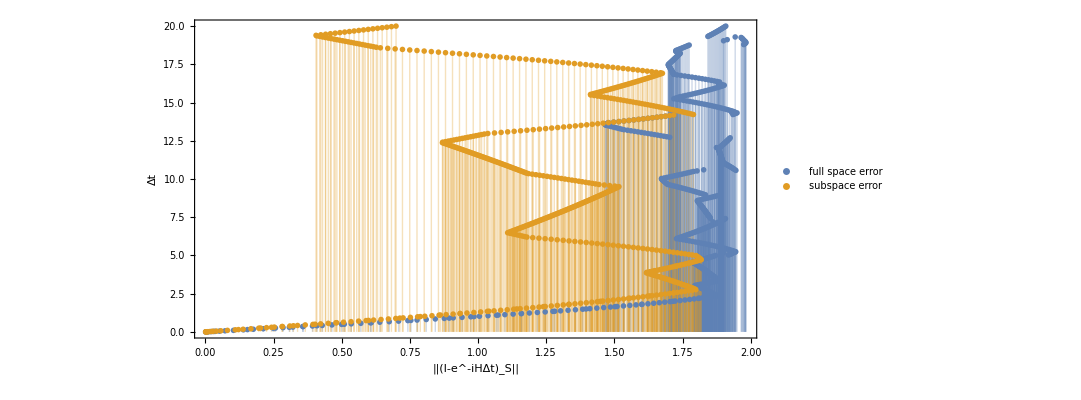

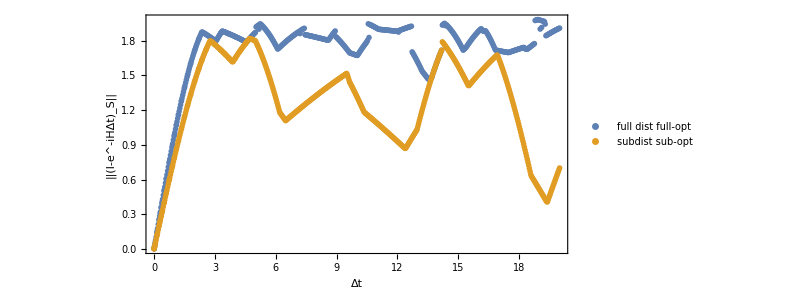

```mathematica
triv=ListPlot[{Transpose@{Values[disttoid][[All,"fullopt"]],Keys@disttoid},Transpose@{Values[disttoid][[All,"subopt"]],Keys@disttoid}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,ImageSize->800,stylebig[2,{"full space error","subspace error"},{0.15,0.7}]]

ListPlot[{Transpose@{Keys@disttoid,Values[disttoid][[All,"fullopt"]]},Transpose@{Keys@disttoid,Values[disttoid][[All,"subopt"]]}},FrameLabel->{"Δt",TraditionalForm["||(I-e^-iHΔt)_S||"]},stylebig[2,{"full dist full-opt","subdist sub-opt"},{0.6,0.2}]]
```

```mathematica
Export["/home/cica/chemistry/img/triv.pdf",triv];
```

### Load data

Get best results with distance at least 0.001 (subspace distance) from recompilation

```mathematica
times={0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

```mathematica
fullcompdist<<fullcompdist.mx;
subcompdist<<subcompdist.mx;
```

### Subspace distance comparison “subopt”

The “sd” stands for subspace-distance, and “fd” indicates fullspace-distance

```mathematica
mindist=1*10^-3;
disttype="subopt";
```

```mathematica
sdsubcomp=<|Table[t->First@MinimalBy[MinimalBy[Select[subcompdist[t],#["dist"][disttype]<=mindist&],#["ngates"]&],#["dist"][disttype]&],{t,times}]|>;
sdfullcomp=<|Table[t->First@MinimalBy[MinimalBy[Select[fullcompdist[t],#["dist"][disttype]<=mindist&],#["ngates"]&],#["dist"][disttype]&],{t,times}]|>;
(*indicate the fail results*)
Print["failed runs on subspace-compiled for Δt:",Select[sdsubcomp,Length@#===1&]//Keys];
Print["failed runs on full space-compiled for Δt:",Select[sdfullcomp,Length@#===1&]//Keys];

(*select the successfull results only*)
bestsubcomp=Select[sdsubcomp,Length@#>1&];
bestfullcomp=Select[sdfullcomp,Length@#>1&];
```

failed runs on subspace-compiled for Δt:{}

failed runs on full space-compiled for Δt:{}

Get a set of times where all efforts work for a fair comparison

```mathematica
times2=Complement[times,{0.007,0.035}]
```

{0.001,0.002,0.005,0.01,0.02,0.03,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

All Trotter results with distance at most 0.001 (subspace and full-space distances)

```mathematica
sdtrot=<|Table[t->Select[Flatten[Values[trotsumsubplus[t]],1],#[[2]]<=mindist&],{t,times}]|>;
fdtrot=<|Table[t->Select[Flatten[Values[trotsum[t]],1],#[[2]]<=mindist&],{t,times}]|>;
```

```mathematica
besttrotsub=<|Table[t->First@MinimalBy[MinimalBy[Select[{Total@#[[1]],#[[2]]}&/@Flatten[Values@trotsumsub[t],1],#[[2]]<=mindist&],#[[1]]&],#[[2]]&],{t,times}]|>;
```

Pick the closest distance of trotterization with minimal number of gates
subspace-recompiled vs trotterization with subspace distance <= 10^-3

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
times2//Length
```

37

```mathematica
style[ndata_,legends_,legendpos_]:={AspectRatio->2/3,ImageSize->550,
LabelStyle->{FontFamily->"FreeSerif",FontSize->20,Background->None},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,23,FontFamily->"FreeSerif"],
PlotStyle->Reverse@rainbowcol[ndata],PlotMarkers->{"OpenMarkersThick",8},Background->White,PlotLegends->Placed[PointLegend[Automatic,legends,Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],
legendpos],PlotRange->All,GridLinesStyle->Directive[Black, Dashed]};
```

```mathematica
sdplotsubcomp=With[{m=Max[#&/@bestsubcomp⟦All,"ngates"⟧]},Table[{t,bestsubcomp[t]["ngates"]},{t,times2}]/.{{d_,m}:>Labeled[{d,m},m,Below,Background->None]}];
sdplotfullcomp=With[{m=Max[#&/@bestfullcomp⟦All,"ngates"⟧]},Table[{t,bestfullcomp[t]["ngates"]},{t,times2}]/.{{d_,m}:>Labeled[{d,m},m,Below,Background->None]}];
sdplottrotsub=With[{m=Max[besttrotsub⟦All,1⟧]},Table[{t,besttrotsub[t][[1]]},{t,times2}]/.{{d_,m}:>Labeled[{d,m},m,Below,Background->None]}];
```

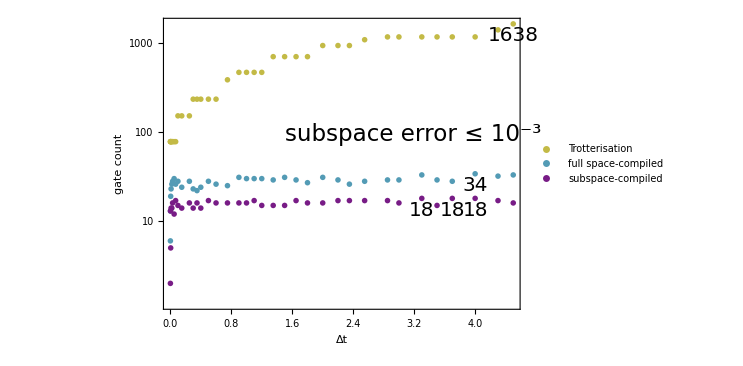

```mathematica
subdistplot=ListLogPlot[{sdplottrotsub,sdplotfullcomp,sdplotsubcomp},FrameLabel->{"Δt","gate count"},GridLines->{None, {18,34,1638}},style[3,{"Trotterisation","full space-compiled","subspace-compiled"},{0.79,0.13}],
Epilog->Text[Style["subspace error ≤ 10^-3",23,FontFamily->"FreeSerif",Background->White],Scaled[{.7,.6}]]]
```

```mathematica
Export["/home/cica/chemistry/img/subspace_distance.pdf",subdistplot];
```

Plot by the triviality of the unitary

```mathematica
disttype="subopt";
sdtrivplotsubcomp=Table[{disttoid[N@t][disttype],bestsubcomp[t]["ngates"]},{t,times2}];
sdtrivplotfullcomp=Table[{disttoid[N@t][disttype],bestfullcomp[t]["ngates"]},{t,times2}];
sdtrivplottrotsub=Table[Labeled[{disttoid[N@t][disttype],besttrotsub[t][[1]]},t,Above,Background->None],{t,times2}]
```

{Labeled[{0.000810213,78},0.001,Above,Background→None],Labeled[{0.00162043,78},0.002,Above,Background→None],Labeled[{0.00405106,78},0.005,Above,Background→None],Labeled[{0.00810211,78},0.01,Above,Background→None],Labeled[{0.0162041,78},0.02,Above,Background→None],Labeled[{0.0243058,78},0.03,Above,Background→None],Labeled[{0.0405079,78},0.05,Above,Background→None],Labeled[{0.0567073,78},0.07,Above,Background→None],Labeled[{0.0809992,152},0.1,Above,Background→None],Labeled[{0.121457,152},0.15,Above,Background→None],Labeled[{0.202207,152},0.25,Above,Background→None],Labeled[{0.242466,234},0.3,Above,Background→None],Labeled[{0.282625,234},0.35,Above,Background→None],Labeled[{0.322669,234},0.4,Above,Background→None],Labeled[{0.402342,234},0.5,Above,Background→None],Labeled[{0.481355,234},0.6,Above,Background→None],Labeled[{0.598354,386},0.75,Above,Background→None],Labeled[{0.713144,468},0.9,Above,Background→None],Labeled[{0.788234,468},1,Above,Background→None],Labeled[{0.86203,468},1.1,Above,Background→None],Labeled[{0.934412,468},1.2,Above,Background→None],Labeled[{1.04007,702},1.35,Above,Background→None],Labeled[{1.1419,702},1.5,Above,Background→None],Labeled[{1.2395,702},1.65,Above,Background→None],Labeled[{1.33253,702},1.8,Above,Background→None],Labeled[{1.44887,936},2,Above,Background→None],Labeled[{1.5557,936},2.2,Above,Background→None],Labeled[{1.62916,936},2.35,Above,Background→None],Labeled[{1.7177,1088},2.55,Above,Background→None],Labeled[{1.78837,1170},2.85,Above,Background→None],Labeled[{1.76596,1170},3,Above,Background→None],Labeled[{1.718,1170},3.3,Above,Background→None],Labeled[{1.68374,1170},3.5,Above,Background→None],Labeled[{1.64769,1170},3.7,Above,Background→None],Labeled[{1.64856,1170},4,Above,Background→None],Labeled[{1.72643,1404},4.3,Above,Background→None],Labeled[{1.7733,1638},4.5,Above,Background→None]}

```mathematica
SortBy[Table[{disttoid[N@t][disttype],t,besttrotsub[t][[1]]},{t,times2}],#[[2]]&]
```

{{0.000810213,0.001,78},{0.00162043,0.002,78},{0.00405106,0.005,78},{0.00810211,0.01,78},{0.0162041,0.02,78},{0.0243058,0.03,78},{0.0405079,0.05,78},{0.0567073,0.07,78},{0.0809992,0.1,152},{0.121457,0.15,152},{0.202207,0.25,152},{0.242466,0.3,234},{0.282625,0.35,234},{0.322669,0.4,234},{0.402342,0.5,234},{0.481355,0.6,234},{0.598354,0.75,386},{0.713144,0.9,468},{0.788234,1,468},{0.86203,1.1,468},{0.934412,1.2,468},{1.04007,1.35,702},{1.1419,1.5,702},{1.2395,1.65,702},{1.33253,1.8,702},{1.44887,2,936},{1.5557,2.2,936},{1.62916,2.35,936},{1.7177,2.55,1088},{1.78837,2.85,1170},{1.76596,3,1170},{1.718,3.3,1170},{1.68374,3.5,1170},{1.64769,3.7,1170},{1.64856,4,1170},{1.72643,4.3,1404},{1.7733,4.5,1638}}

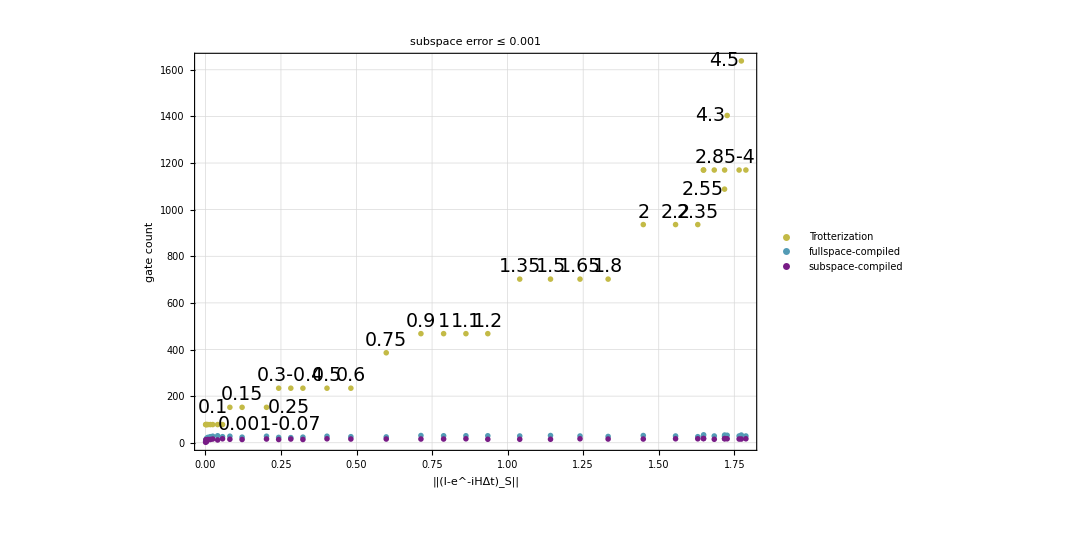

```mathematica
sdtrivplottrotsub={{0.0008102132316433245,78},{0.0016204263303208895,78},{0.0040510634989113685,78},{0.008102110377188072,78},{0.016204087789706955,78},{0.02430579927507008,78},{0.040507892638385466,78},Labeled[{0.05670732689379351,78},"0.001-0.07",Right,Background->None],Labeled[{0.0809991663296603,152},0.1,Left,Background->None],Labeled[{0.12145720894488461,152},0.15,Above,Background->None],Labeled[{0.20220722740879965,152},0.25,Right,Background->None],{0.2424660743979451,234},Labeled[{0.2826254461835413,234},"0.3-0.4",Above,Background->None],{0.3226688668041592,234},Labeled[{0.40234219529810206,234},0.5,Above,Background->None],Labeled[{0.48135532476227,234},0.6,Above,Background->None],Labeled[{0.5983538810723553,386},0.75,Above,Background->None],Labeled[{0.7131436918438683,468},0.9,Above,Background->None],Labeled[{0.7882335183438376,468},1,Above,Background->None],Labeled[{0.862029940845611,468},1.1,Above,Background->None],Labeled[{0.9344118675842841,468},1.2,Above,Background->None],Labeled[{1.0400734498574635,702},1.35,Above,Background->None],Labeled[{1.1418957362476472,702},1.5,Above,Background->None],Labeled[{1.2395028630262224,702},1.65,Above,Background->None],Labeled[{1.3325345261780437,702},1.8,Above,Background->None],Labeled[{1.448868392126713,936},2,Above,Background->None],Labeled[{1.5556964282299883,936},2.2,Above,Background->None],Labeled[{1.6291551517221055,936},2.35,Above,Background->None],Labeled[{1.717701605597373,1088},2.55,Left,Background->None],{1.78836875406648,1170},{1.7659617157243275,1170},Labeled[{1.7179996131446926,1170},"2.85-4",Above,Background->None],{1.6837391150583916,1170},{1.647692134654776,1170},{1.6485623285253044,1170},Labeled[{1.7264274196577911,1404},4.3,Left,Background->None],Labeled[{1.7732980651752697,1638},4.5,Left,Background->None]};

subtriv=ListPlot[{sdtrivplottrotsub,sdtrivplotfullcomp,sdtrivplotsubcomp},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"gate count"},LabelStyle->{FontFamily->"FreeSerif",FontSize->19,Background->None},ImageSize->800,style[3,{"Trotterization","fullspace-compiled","subspace-compiled"},{0.2,0.75}],PlotLabel->"subspace error ≤ 0.001",GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/subspace_trivial.pdf",subtriv];
```

data structure for trotsum, trotsumsub: {{twos, singles}, dist, 1-entfid, energy_diff, 1-entstate}

### Fullspace distance comparison “fullopt”

The “sd” stands for subspace-distance, and “fd” indicates fullspace-distance

```mathematica
mindist=1*10^-3;
```

```mathematica
disttype="fullopt";
fdfullcomp=<|Table[t->First@MinimalBy[MinimalBy[Select[fullcompdist[t],#["dist"][disttype]<=mindist&],#["ngates"]&],#["dist"][disttype]&],{t,times}]|>;
(*indicate the fail results*)
Print["failed runs on fullspace-compiled for Δt:",Select[fdfullcomp,Length@#===1&]//Keys];

(*select the successfull results only*)
bestfullcompf=Select[fdfullcomp,Length@#>1&];
```

failed runs on fullspace-compiled for Δt:{}

Get a set of times where all efforts work for a fair comparison

```mathematica
times
times2=Complement[times,{0.007,0.035}]
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

{0.001,0.002,0.005,0.01,0.02,0.03,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

All Trotter results with distance at most 0.001 (subspace and full-space distances)

```mathematica
fdtrot=<|Table[t->Select[Flatten[Values[trotsum[t]],1],#[[2]]<=mindist&],{t,times}]|>;
```

```mathematica
besttrotfull=<|Table[t->First@MinimalBy[MinimalBy[Select[{Total@#[[1]],#[[2]]}&/@Flatten[Values@trotsum[t],1],#[[2]]<=mindist&],#[[1]]&],#[[2]]&],{t,times}]|>;
```

Pick the closest distance of trotterization with minimal number of gates
subspace-recompiled vs trotterization with subspace distance <= 10^-3

```mathematica
fdplotfullcomp=With[{m=Max[#&/@bestfullcompf⟦All,"ngates"⟧]},Table[{t,bestfullcompf[t]["ngates"]},{t,times2}]/.{{d_,m}->Labeled[{d,m},m,Below,Background->None]}];
fdplottrotsub=With[{m=Max[besttrotfull⟦All,1⟧]},Table[{t,besttrotfull[t][[1]]},{t,times2}]/.{{d_,m}->Labeled[{d,m},m,Below,Background->None]}];
```

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

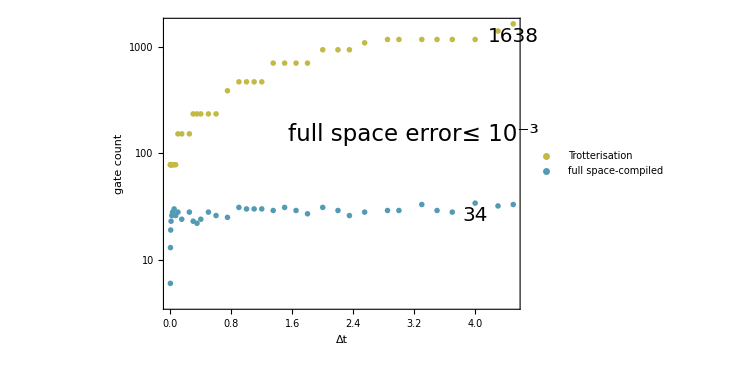

```mathematica
fulldistplot=ListLogPlot[{fdplottrotsub,fdplotfullcomp},FrameLabel->{"Δt","gate count"},GridLines->{None, {34,1638}},style[3,{"Trotterisation","full space-compiled"},{0.79,0.1}],
Epilog->Text[Style["full space error≤ 10^-3",23,FontFamily->"FreeSerif",Background->White],Scaled[{.7,.6}]]]
```

```mathematica
Export["/home/cica/chemistry/img/fullspace_distance.pdf",fulldistplot];
```

Plot by the triviality of the unitary

```mathematica
disttype="fullopt"
fdtrivplotfullcomp=Table[{disttoid[N@t][disttype],bestfullcomp[t]["ngates"]},{t,times2}];
fdtrivplottrotfull=Table[Labeled[{disttoid[N@t][disttype],besttrotfull[t][[1]]},t,Above,Background->None],{t,times2}];
```

fullopt

```mathematica
Export["/home/cica/chemistry/img/fullspace_trivial.pdf",fulltriv];
```

### Recompilation statistics

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/dynamics

```mathematica
color={RGBColor[0.7285450767713475, 0.03494508851712408, 0.14198068147566834],RGBColor[0.4582847199296809, 0.6086754253762674, 0.6585971050832811]}
```

{RGBColor[0.7285450767713475, 0.03494508851712408, 0.14198068147566834],RGBColor[0.4582847199296809, 0.6086754253762674, 0.6585971050832811]}

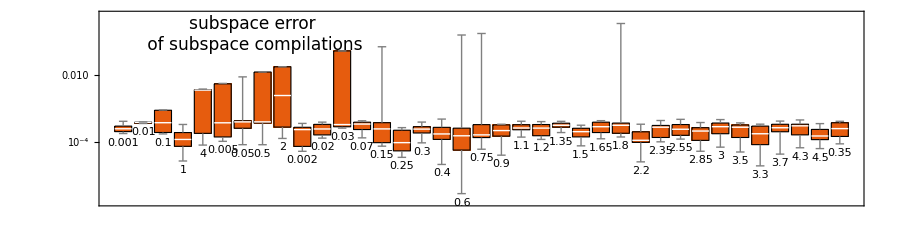

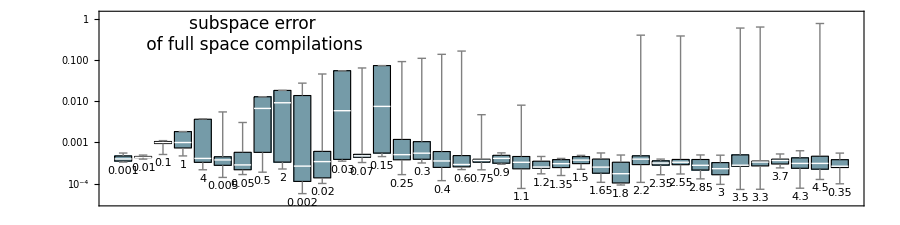

```mathematica
sd1=BoxWhiskerChart[Table[subcompdist[t][[All,"dist"]][[All,"subopt"]],{t,Sort@times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["subspace error\n of subspace compilations",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{10,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]}
]
sd2=BoxWhiskerChart[Table[fullcompdist[t][[All,"dist"]][[All,"subopt"]],{t,Sort@times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["subspace error\n of full space compilations",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{10,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]}
]
```

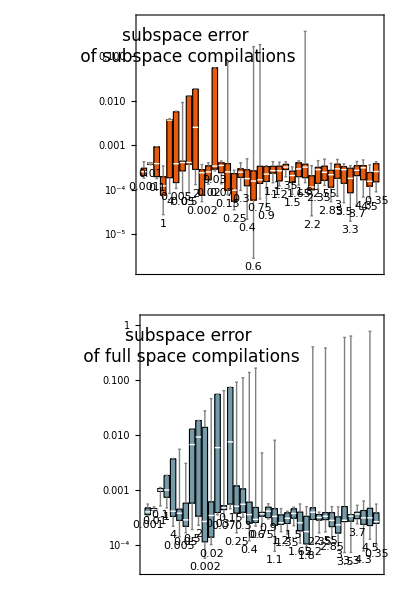

```mathematica
Column[{sd1,sd2},Frame->True,Background->White,ImageMargins->-1]
```

```mathematica
Export["/home/cica/chemistry/img/subdists.pdf",%]
```

/home/cica/chemistry/img/subdists.pdf

```mathematica
Export["/home/cica/chemistry/img/hammat.pdf",%]
```

/home/cica/chemistry/img/hammat.pdf

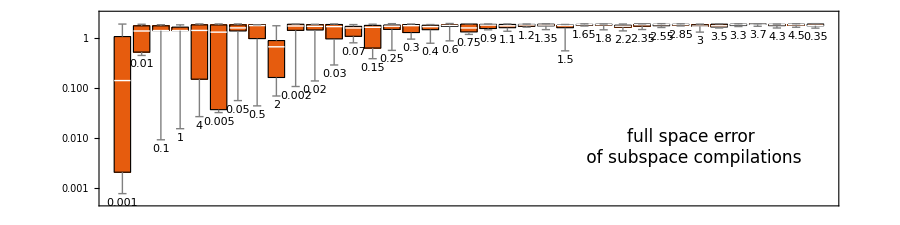

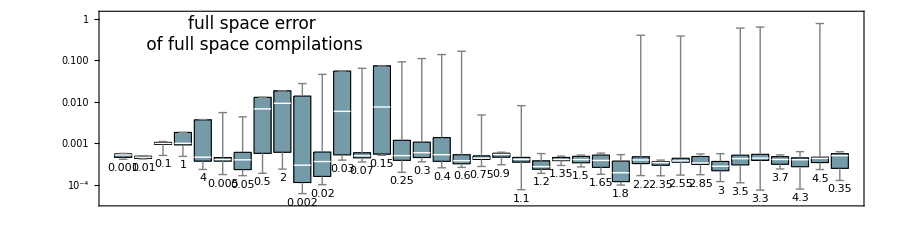

```mathematica
fd1=BoxWhiskerChart[Table[subcompdist[t][[All,"dist"]][[All,"fullopt"]],{t,Sort@times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["full space error\n of subspace compilations",17,FontFamily->"FreeSerif",Background->White],Scaled[{.8,.3}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{10,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]}
]
fd2=BoxWhiskerChart[Table[fullcompdist[t][[All,"dist"]][[All,"fullopt"]],{t,Sort@times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["full space error\n of full space compilations",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{10,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]}
]
```

```mathematica
Export["/home/cica/chemistry/img/fulldists.pdf",Row[{fd1,fd2},Frame->True,Background->White,ImageMargins->-1]]
```

/home/cica/chemistry/img/fulldists.pdf

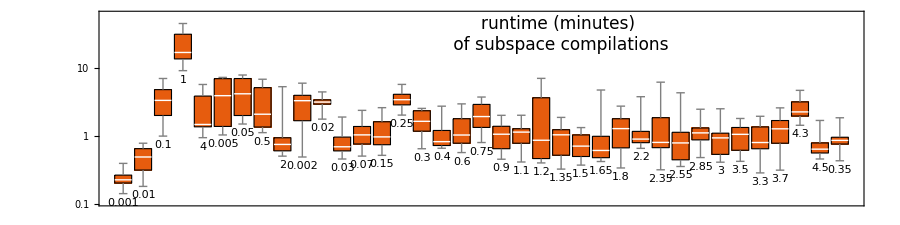

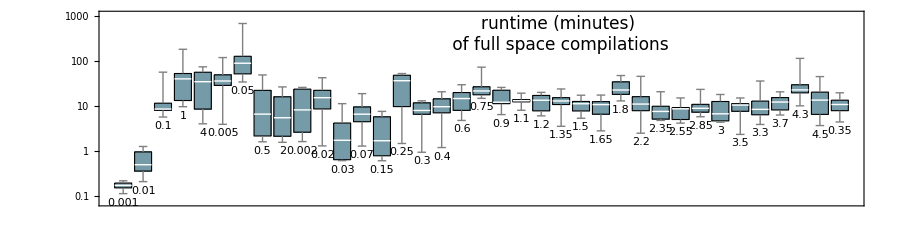

```mathematica
runsub=BoxWhiskerChart[Table[ressubH2[t][[All,4]],{t,Sort@times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["runtime (minutes)\n of subspace compilations",17,FontFamily->"FreeSerif",Background->White],Scaled[{.6,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{10,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]}
]
runfull=BoxWhiskerChart[Table[resfullH2[t][[All,4]],{t,Sort@times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["runtime (minutes)\n of full space compilations",17,FontFamily->"FreeSerif",Background->White],Scaled[{.6,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{10,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]}
]
```

```mathematica
Export["/home/cica/chemistry/img/runtimes.pdf",Column[{runsub,runfull},Frame->True,Background->White,ImageMargins->-1]]
```

/home/cica/chemistry/img/runtimes.pdf

Successful results by the  distance criteria

```mathematica
sucsubsubcomp=<|Table[t->Select[subcompdist[t],#["dist"]["subopt"]<=10^-3&],{t,times}]|>;
sucsubfullcomp=<|Table[t->Select[fullcompdist[t],#["dist"]["subopt"]<=10^-3&],{t,times}]|>;
sucsubsubcompfrac=<|Table[t->N[Length[sucsubsubcomp[t]]/Length[subcompdist[t]]],{t,times}]|>;
sucsubfullcompfrac=<|Table[t->N[Length[sucsubfullcomp[t]]/Length[fullcompdist[t]]],{t,times}]|>;
sucfullfullcomp=<|Table[t->Select[fullcompdist[t],#["dist"]["fullopt"]<=10^-3&],{t,times}]|>;
sucfullfullcompfrac=<|Table[t->N[Length[sucfullfullcomp[t]]/Length[fullcompdist[t]]],{t,times}]|>;
```

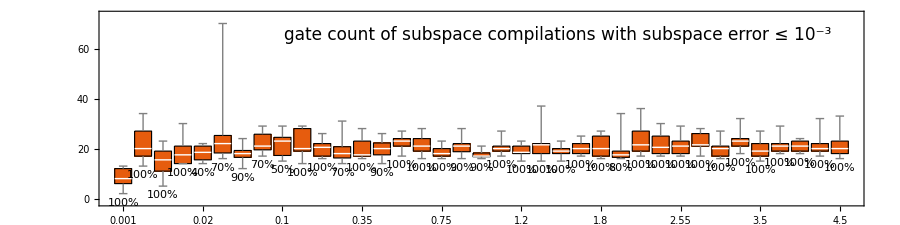

/home/cica/chemistry/img/gatesuberrsubcomp.pdf

```mathematica
Table[Labeled[sucsubsubcomp[t][[All,"ngates"]],ToString[IntegerPart[sucsubsubcompfrac[t]*100]]<>"%",Below],{t,Sort@times}];

BoxWhiskerChart[%,FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[Sort@times,Axis,Rotate[#,Pi/4]&],PlotTheme->"Scientific",Epilog->Text[Style["gate count of subspace compilations with subspace error ≤ 10^-3",17,FontFamily->"FreeSerif",Background->White],Scaled[{.6,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{40,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]},ImageSize->Large
]

Export["/home/cica/chemistry/img/gatesuberrsubcomp.pdf",%]
```

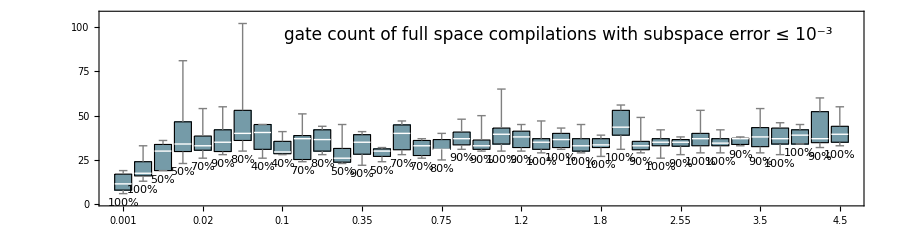

/home/cica/chemistry/img/gatesuberrfullcomp.pdf

```mathematica
Table[Labeled[sucsubfullcomp[t][[All,"ngates"]],ToString[IntegerPart[sucsubfullcompfrac[t]*100]]<>"%",Below],{t,Sort@times}];

BoxWhiskerChart[%,FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[Sort@times,Axis,Rotate[#,Pi/4]&],PlotTheme->"Scientific",Epilog->Text[Style["gate count of full space compilations with subspace error ≤ 10^-3",17,FontFamily->"FreeSerif",Background->White],Scaled[{.6,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{40,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]},ImageSize->Large
]
Export["/home/cica/chemistry/img/gatesuberrfullcomp.pdf",%]
```

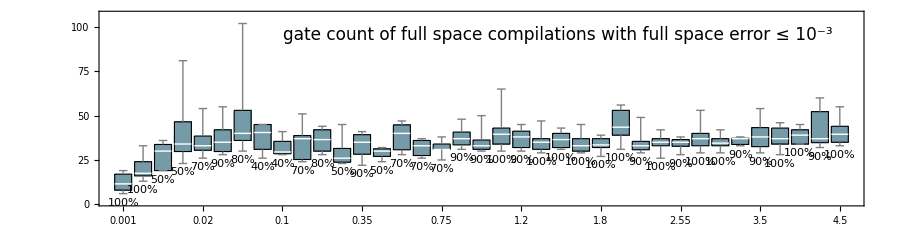

/home/cica/chemistry/img/gatefullerrfullcomp.pdf

```mathematica
Table[Labeled[sucfullfullcomp[t][[All,"ngates"]],ToString[IntegerPart[sucfullfullcompfrac[t]*100]]<>"%",Below],{t,Sort@times}];

BoxWhiskerChart[%,FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[Sort@times,Axis,Rotate[#,Pi/4]&],PlotTheme->"Scientific",Epilog->Text[Style["gate count of full space compilations with full space error ≤ 10^-3",17,FontFamily->"FreeSerif",Background->White],Scaled[{.6,.88}]],ImageSize->900,AspectRatio->1/4,
ImagePadding->{{50,10},{40,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]},ImageSize->Large
]
Export["/home/cica/chemistry/img/gatefullerrfullcomp.pdf",%]
```